```mathematica
Quit[]
```

## Definition of subtraction terms in Minkowski

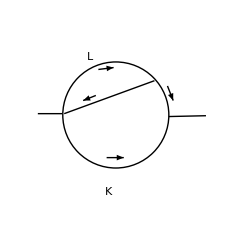

```mathematica
SetAttributes[Dot,Orderless];
```

```mathematica
PropExp[k_,p_,m_,mUV_,λ_,x_]:=x-2 c x^2-d x^2+4 c^2 x^3+4 c d x^3+d^2 x^3-8 c^3 x^4-12 c^2 d x^4-6 c d^2 x^4-d^3 x^4+16 c^4 x^5+32 c^3 d x^5+24 c^2 d^2 x^5+8 c d^3 x^5+d^4 x^5-32 c^5 x^6-80 c^4 d x^6-80 c^3 d^2 x^6-40 c^2 d^3 x^6-10 c d^4 x^6-d^5 x^6+64 c^6 x^7+192 c^5 d x^7+240 c^4 d^2 x^7+160 c^3 d^3 x^7+60 c^2 d^4 x^7-128 c^7 x^8-448 c^6 d x^8-672 c^5 d^2 x^8-560 c^4 d^3 x^8+256 c^8 x^9+1024 c^7 d x^9+1792 c^6 d^2 x^9-512 c^9 x^10-2304 c^8 d x^10+1024 c^10 x^11 + ALARM λ^11 /.{c->If[p===0,0,λ k.p],d->λ ^2 (If[p===0,0,p.p]+mUV^2-m^2) }
Taylor[x_,λt_,order_]:=TensorExpand[Normal[Series[x,{λt,0,order}]]/.{λt->1}];
```

```mathematica
FullSubtraction[k_,l_,p_,m_,mUV_,lpow_] :=
Taylor[PropExp[k,0,m,mUV,λkl,xk]PropExp[k,-p,m,mUV,λkl,xk]PropExp[l,0,m,mUV,λkl,xl]PropExp[k+l,-p,m,mUV,λkl,xkl],λkl,2lpow] /.{xl->1/(l.l-mUV^2),xk->1/(k.k-mUV^2), xkl->1/((k+l).(k+l)-mUV^2)}
BubbleSubtraction[k_,l_,p_,m_,mUV_,lpow_] :=Taylor[PropExp[l,0,m,mUV,λl,xl]PropExp[l,k-p,m,mUV,λl,xl],λl,lpow]/((k.k-m^2)( (k-p).(k-p)-m^2))/.{xl->1/(l.l-mUV^2)} ;
TriangleSubtraction[k_,l_,p_,m_,mUV_,lpow_] :=Taylor[PropExp[k,0,m,mUV,λk,xk]PropExp[k,-p,m,mUV,λk,xk]PropExp[-k,l+k,m,mUV,λk,xk],λk,lpow-2]/((l+k-p).(l+k-p)-m^2)/.{xk->1/(k.k-mUV^2)} ;
DoubleBubbleSubtraction[k_,l_,p_,m_,mUV_,lpow_] :=Module[{bubble},
bubble=Taylor[PropExp[l,0,m,mUV,λl,xl]PropExp[l,k-p,m,mUV,λl,xl],λl,lpow]/.{p.p-> λk^2 p.p, p.p1__-> λk p.p1,p1__.p->λk p.p1, mUV->λk mUV,m->λk m}; (* expand in small mass too*)
Taylor[bubble PropExp[k,0,m,mUV,λk,xk]PropExp[k,-p,m,mUV,λk,xk],λk,2lpow]/.{xk->1/(k.k-mUV^2),xl->1/(l.l-mUV^2)}
];
TriangleBubbleSubtraction[k_,l_,p_,m_,mUV_,lpow_] :=Module[{triangle},
triangle=Taylor[PropExp[k,0,m,mUV,λk,xk]PropExp[k,-p,m,mUV,λk,xk]PropExp[-k,k+l,m,mUV,λk,xk],λk,lpow-2]/.{mUV->λl mUV,m->λl m, p.p-> λl^2 p.p,p.p1__-> λl p.p1,p1__.p->λl p.p1};
Taylor[triangle PropExp[k+l,-p,m,mUV,λl,xl],λl,lpow 2]/.{xk->1/(k.k-mUV^2),xl->1/((l+k).(l+k)-mUV^2)} (*inflated expansion: 2*lpow *)
];
FiniteIntegrand[k_,l_,p_,m_,mUV_,lpow_] :=1/((l.l-m^2)( k.k -m^2)((k+l-p).(k+l-p)-m^2)((k-p).(k-p)-m^2))-FullSubtraction[k,l,p,m,mUV,lpow]-BubbleSubtraction[k,l,p,m,mUV,lpow]-TriangleSubtraction[k,l,p,m,mUV,lpow] +DoubleBubbleSubtraction[k,l,p,m,mUV,lpow]+TriangleBubbleSubtraction[k,l,p,m,mUV,lpow];
V={k->{1,0,0,0},l->λ{0,0,0,1},p->{1,0,0,1},lpow->2,mUV->2,mIN->0};
Print["Unsubtracted: ",Series[λ^4 (l.p)^lpow/((l.l-mIN^2)( k.k -mIN^2)((k+l-p).(k+l-p)-mIN^2)( (k-p).(k-p)-mIN^2))/.V,{λ,Infinity,1}]]
Print["Double limit: ",Series[-λ^4 (l.p)^lpow FullSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Bubble      : ",Series[ -λ^4 (l.p)^lpow BubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Double bubbl: ",Series[ λ^4 (l.p)^lpow DoubleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Triangle    : ",Series[ -λ^4 (l.p)^lpow TriangleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Tri bub     : ",Series[ λ^4 (l.p)^lpow TriangleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Result      : ",Series[ λ^4 (l.p)^lpow FiniteIntegrand[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
```

Unsubtracted: λ^2+2 λ+3+4/λ+O((1/λ)^2)

Double limit: -(985 λ^2)/729-(14 λ)/243-4939/729-812/(243 λ)+O((1/λ)^2)

Bubble      : -λ^2-2 λ-3-24/λ+O((1/λ)^2)

Double bubbl: (985 λ^2)/729+(14 λ)/243+4939/729+56/(81 λ)+O((1/λ)^2)

Triangle    : λ^4/27+(2 λ^3)/27+λ^2/9+(4 λ)/27+5/27+2/(9 λ)+O((1/λ)^2)

Tri bub     : -λ^4/27-(2 λ^3)/27-λ^2/9-(4 λ)/27-5/27+50/(27 λ)+O((1/λ)^2)

Result      : -5000/(243 λ)+O((1/λ)^2)

```mathematica
V={k->λ{1,0,0,0},l->λ{-1,0,0,0}+{1,1,0,0},p->{1,0,0,1},lpow->2,mUV->2,mIN->1/2};
Print["Unsubtracted: ",Series[λ^4 (l.p)^lpow/((l.l-mIN^2)( k.k -mIN^2)((k+l-p).(k+l-p)-mIN^2)( (k-p).(k-p)-mIN^2))/.V,{λ,Infinity,1}]]
Print["Double limit: ",Series[-λ^4 (l.p)^lpow FullSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Bubble      : ",Series[ -λ^4 (l.p)^lpow BubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Double bubbl: ",Series[ λ^4 (l.p)^lpow DoubleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Triangle    : ",Series[ -λ^4 (l.p)^lpow TriangleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Tri bub     : ",Series[ λ^4 (l.p)^lpow TriangleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Result      : ",Series[ λ^4 (l.p)^lpow FiniteIntegrand[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
```

Unsubtracted: 4/7+8/(7 λ)+O((1/λ)^2)

Double limit: 961/128-23/(8 λ)+O((1/λ)^2)

Bubble      : O((1/λ)^2)

Double bubbl: O((1/λ)^2)

Triangle    : -4/7+8/(7 λ)+O((1/λ)^2)

Tri bub     : -961/128+961/(64 λ)+O((1/λ)^2)

Result      : 6463/(448 λ)+O((1/λ)^2)

```mathematica
V={k->λ{1,0,0,0},l->{0,0,0,1},p->{1,0,0,1},lpow->2,mUV->2,mIN->1/2};
Print["Unsubtracted: ",Series[λ^4 (l.p)^lpow/((l.l-mIN^2)( k.k -mIN^2)((k+l-p).(k+l-p)-mIN^2)( (k-p).(k-p)-mIN^2))/.V,{λ,Infinity,1}]]
Print["Double limit: ",Series[-λ^4 (l.p)^lpow FullSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Bubble      : ",Series[ -λ^4 (l.p)^lpow BubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Double bubbl: ",Series[ λ^4 (l.p)^lpow DoubleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Triangle    : ",Series[ -λ^4 (l.p)^lpow TriangleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Tri bub     : ",Series[ λ^4 (l.p)^lpow TriangleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Result      : ",Series[ λ^4 (l.p)^lpow FiniteIntegrand[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
```

Unsubtracted: O((1/λ)^2)

Double limit: O((1/λ)^2)

Bubble      : -λ^2/27-31/81-121/(162 λ)+O((1/λ)^2)

Double bubbl: λ^2/27+31/81+121/(162 λ)+O((1/λ)^2)

Triangle    : O((1/λ)^4)

Tri bub     : O((1/λ)^4)

Result      : O((1/λ)^2)

```mathematica
V={k->λ{1,0,0,0},l->λ{0,0,0,1},p->{1,0,0,1},lpow->2,mUV->2,mIN->1/2};
Print["Unsubtracted: ",Series[λ^8 (l.p)^lpow/((l.l-mIN^2)( k.k -mIN^2)((k+l-p).(k+l-p)-mIN^2)( (k-p).(k-p)-mIN^2))/.V,{λ,Infinity,1}]]
Print["Double limit: ",Series[-λ^8 (l.p)^lpow FullSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Bubble      : ",Series[ -λ^8(l.p)^lpow BubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Double bubbl: ",Series[ λ^8 (l.p)^lpow DoubleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Triangle    : ",Series[ -λ^8 (l.p)^lpow TriangleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Tri bub     : ",Series[ λ^8 (l.p)^lpow TriangleBubbleSubtraction[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
Print["Result      : ",Series[ λ^8 (l.p)^lpow FiniteIntegrand[k,l,p,mIN,mUV,lpow/.V]/.V,{λ,Infinity,1}]]
```

Unsubtracted: λ^2/2+2 λ+79/16+73/(8 λ)+O((1/λ)^2)

Double limit: -λ^2/2-2 λ-79/16-73/(8 λ)+O((1/λ)^2)

Bubble      : -4 λ+3/2-39/λ+O((1/λ)^2)

Double bubbl: 4 λ-3/2+39/λ+O((1/λ)^2)

Triangle    : -λ^2/2-λ-121/16-57/(4 λ)+O((1/λ)^2)

Tri bub     : λ^2/2+λ+121/16+57/(4 λ)+O((1/λ)^2)

Result      : O((1/λ)^3)

## cLTD helper resources

```mathematica
Import["/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/alphaloop/Mathematica/cLTD.m"]
```

Compute the correpsonding cLTD expression using FORM.
Input Format:
The scalar propagator of the expression must be expressed as: 
	-> prop[4momentum,mass] (e.g. prop[k1+p1,0])
Outside of prop[] the presence of a momentum not contracted 
into a dot product will be considered as being its energy component 

Options: {
          "FORMpath"→"form",
          "WorkingDirectory"→Directory[],
          "aLPath"->"PathTo/Your/AlphaLoop/Installation/",
          "loopmom"->{loopmomsymbol1,loopmomsymbol2,...} (default: {k1,k2,k3,k4})
}

Example:
 expr = k1 prop[k1-p1,0]prop[k1-p2,0] - k1.p1 p1.p2 p1 prop[k1-p3,m]prop[k1-p4,m] prop[k1-p5,m]
=> cLTD[expr]

WARNING: when summing multiple diagrams they must contain the same 
         number of loops, if this is not possible then call cLTD[] 
         for each of them individually.

Output:
  { cLTD expression, Energies definition} 
  The expression contains the den[] and cLTDnorm[] function which are to be evaluated as 
		den[a_] :> 1/a, cLTDnorm[a_] :> 1/a

p1::shdw: Symbol p1 appears in multiple contexts {cLTD`,Global`}; definitions in context cLTD` may shadow or be shadowed by other definitions.

m::shdw: Symbol m appears in multiple contexts {cLTD`,Global`}; definitions in context cLTD` may shadow or be shadowed by other definitions.

p1$::shdw: Symbol p1$ appears in multiple contexts {cLTD`,Global`}; definitions in context cLTD` may shadow or be shadowed by other definitions.

```mathematica
LeadingPower[expr_,var_,OptionsPattern[MaxDepth->30]]:=Max[Table[((term-(term/.{_.var^e__:>0,_. var:>0})))/.{_.var^e__:>e,_. var:>1},{term,List@@(Series[expr,{var,∞,OptionValue[MaxDepth]}]//Normal)}]]
```

```mathematica
DotProductExpansion[k1_,k2_]:=k1 k2 -k1.k2
```

```mathematica
ApplyCLTDToTerm[term_,OptionsPattern[{"apply_cLTD"->True, "loop_momenta"->{k,l}}]]:=Module[
{num, denom},
num=Numerator[term];
denom=Denominator[term];
num = TensorExpand[num/.{Dot[A_,B_]:>DotProductExpansion[A,B]}];
denom=denom/.{(A__.A__-M__^2):>prop[A,M]}/.{(A__.A__):>prop[A,0]};
If[OptionValue["apply_cLTD"],cLTD[num denom,"loopmom"-> OptionValue["loop_momenta"],"FORMpath"->"/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/alphaloop/libraries/form/bin/form"],num denom]/.{den[x_]:>1/x}/.{cLTDnorm[x_]:>1/x}
]
```

```mathematica
ApplyCLTDToExpr[expr_]:=
((cLTD[
Total[Table[ApplyCLTDToTerm[term,"apply_cLTD"->False],{term ,(List@@expr)}]],
"loopmom"->{k,l},"FORMpath"->"/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/alphaloop/libraries/form/bin/form"
]/.{den[x_]:>1/x,cLTDnorm[x_]:>1/x,Dot[p,p]:>Dot[pv,pv]})/.Dot[p,x_]:>Dot[pv,x])/.{p->p0};
```

Now the limits

```mathematica
LimitL[Energies_]:=Module[
{
DoTProdSubstitution={k.pv->3,l.pv->7,k.l->11,pv.pv->13,k.k->27,l.l->23,mUV^2->17,p0->31}
},
Simplify[Join[(Energies/.{Dot[l,x_]:>λ Dot[l,x]}/.{Dot[l,l]:>λ Dot[l,l]}/.DoTProdSubstitution),
{
k.l->((λ k.l)/.DoTProdSubstitution),
k.pv->(( k.pv)/.DoTProdSubstitution),
k.k->(( k.k)/.DoTProdSubstitution),
l.l->((λ^2 l.l)/.DoTProdSubstitution),
l.pv->((λ l.pv)/.DoTProdSubstitution),
pv.pv->((pv.pv)/.DoTProdSubstitution),
mUV^2->((mUV^2)/.DoTProdSubstitution),
p0->((p0)/.DoTProdSubstitution)
}
],λ>0]
]
```

```mathematica
VectorLimitL[Energies_]:=Module[
{
VectorSubstitions={l->{1,2,3},k->{4,5,6},pv->{7,8,9},p0->11,mUV^2->17}
},
Simplify[Join[
(Energies/.{Dot[l,x_]:>λ Dot[l,x]}/.{Dot[l,l]:>λ Dot[l,l]}/.VectorSubstitions),
{
k->((k)/.
VectorSubstitions),
l->λ((l)/.
VectorSubstitions),
pv->((pv)/.
VectorSubstitions),
p0->((p0)/.
VectorSubstitions),
mUV^2->((mUV^2)/.VectorSubstitions)
}
],λ>0]
]
```

```mathematica
LimitK[Energies_]:=Module[
{
DoTProdSubstitution={k.pv->3,l.pv->7,k.l->11,pv.pv->13,k.k->27,l.l->23,mUV^2->17,p0->31}
},
Simplify[Join[(Energies/.{Dot[k,x_]:>λ Dot[k,x]}/.{Dot[k,k]:>λ Dot[k,k]}/.DoTProdSubstitution),
{
k.l->((λ k.l)/.DoTProdSubstitution),
k.pv->((λ  k.pv)/.DoTProdSubstitution),
k.k->(( λ^2 k.k)/.DoTProdSubstitution),
l.l->(( l.l)/.DoTProdSubstitution),
l.pv->(( l.pv)/.DoTProdSubstitution),
pv.pv->((pv.pv)/.DoTProdSubstitution),
mUV^2->((mUV^2)/.DoTProdSubstitution),
p0->((p0)/.DoTProdSubstitution)
}
],λ>0]
]
```

```mathematica
VectorLimitK[Energies_]:=Module[
{
VectorSubstitions={l->{1,2,3},k->{4,5,6},pv->{7,8,9},p0->11,mUV^2->17}
},
Simplify[Join[
(Energies/.{Dot[k,x_]:>λ Dot[k,x]}/.{Dot[k,k]:>λ Dot[k,k]}/.VectorSubstitions),
{
k->((λ k)/.
VectorSubstitions),
l->((l)/.
VectorSubstitions),
pv->((pv)/.
VectorSubstitions),
p0->((p0)/.
VectorSubstitions),
mUV^2->((mUV^2)/.VectorSubstitions)
}
],λ>0]
]
```

```mathematica
LimitKL[Energies_]:=Module[
{
DoTProdSubstitution={k.pv->3,l.pv->7,k.l->11,pv.pv->13,k.k->27,l.l->23,mUV^2->17,p0->31}
},
Simplify[Join[(Energies/.{Dot[l,x_]:>λ Dot[l,x],Dot[k,x_]:>λ Dot[k,x]}/.{Dot[l,l]:>λ Dot[l,l],Dot[k,k]:>λ Dot[k,k]}/.DoTProdSubstitution),
{
k.l->((λ^2 k.l)/.DoTProdSubstitution),
k.pv->(( λ k.pv)/.DoTProdSubstitution),
k.k->(( λ^2 k.k)/.DoTProdSubstitution),
l.l->((λ^2 l.l)/.DoTProdSubstitution),
l.pv->((λ l.pv)/.DoTProdSubstitution),
pv.pv->((pv.pv)/.DoTProdSubstitution),
mUV^2->((mUV^2)/.DoTProdSubstitution),
p0->((p0)/.DoTProdSubstitution)
}
],λ>0]
]
```

```mathematica
VectorLimitKL[Energies_]:=Module[
{
VectorSubstitions={l->{1,2,3},k->{4,5,6},pv->{7,8,9},p0->11,mUV^2->17}
},
Simplify[Join[
(Energies/.{Dot[l,x_]:>λ Dot[l,x],Dot[k,x_]:>λ Dot[k,x]}/.{Dot[l,l]:>λ Dot[l,l],Dot[k,k]:>λ Dot[k,k]}/.VectorSubstitions),
{
k->λ((k)/.
VectorSubstitions),
l->λ((l)/.
VectorSubstitions),
pv->((pv)/.
VectorSubstitions),
p0->((p0)/.
VectorSubstitions),
mUV^2->((mUV^2)/.VectorSubstitions)
}
],λ>0]
]
```

## Applying cLTD to the case of lpow=0

```mathematica
cLTDResultLpow0 = ApplyCLTDToExpr[FiniteIntegrand[k,l,p,0,mUV,0 ]]
```

{(1/((E2+E5+E6) (E0+E2+E6-p0))+1/((E0+E5+p0) (E2+E5+E6))+1/((E2+E5+E6) (E0+E2+E6+p0))+1/((E0+E5+p0) (E0+E2+E6+p0))+1/((E0+E5-p0) (E2+E5+E6))+1/((E0+E5-p0) (E0+E2+E6-p0)))/(16 E0 E2 E5 E6)+(-1/(E3 (E0+E5+p0))-1/(E3 (E0+E5-p0)))/(16 E0 E3^2 E5)+1/(16 E1^3 E3^3)+(-2/(E1 (E1+E3+E4))-2/(E1+E3+E4)^2)/(16 E1^2 E3 E4),{E0→√(k.k),E1→√(k.k-mUV^2),E2→√(l.l),E3→√(l.l-mUV^2),E4→√(2 k.l+k.k+l.l-mUV^2),E5→√(-2 k.pv+k.k+pv.pv),E6→√(2 k.l-2 k.pv+k.k-2 l.pv+l.l+pv.pv)}}

```mathematica
TogetheredcLTDResultLpow0=Together[cLTDResultLpow0⟦1⟧];
```

```mathematica
LimitL[cLTDResultLpow0⟦2⟧]
```

{E0→3 √3,E1→√10,E2→√23 λ,E3→√(23 λ^2-17),E4→√(23 λ^2+22 λ+10),E5→√34,E6→√(23 λ^2+8 λ+34),k.l→11 λ,k.pv→3,k.k→27,l.l→23 λ^2,l.pv→7 λ,pv.pv→13,mUV^2→17,p0→31}

```mathematica
LeadingPower[Numerator[TogetheredcLTDResultLpow0]/.LimitL[cLTDResultLpow0⟦2⟧],λ]
```

7

```mathematica
LeadingPower[Denominator[TogetheredcLTDResultLpow0]/.LimitL[cLTDResultLpow0⟦2⟧],λ]
```

11

```mathematica
Length[List@@Numerator[TogetheredcLTDResultLpow0]]
```

738

```mathematica
Table[
LeadingPower[(piece)/.LimitL[cLTDResultLpow0⟦2⟧],λ]
, {piece,List@@Numerator[TogetheredcLTDResultLpow0]}
];
Max[%]
```

8

Now apply “on-shell energy subtractions”

```mathematica
SubtractedTogetheredcLTDResultLpow0Numerator = Expand[Expand[(
(Numerator[TogetheredcLTDResultLpow0]/.(
Table[
Ek^t_:>(Simplify[Ek^2/.cLTDResultLpow0⟦2⟧])^((t-Mod[t,2])/2) Ek^Mod[t,2],
{Ek,{E0,E1,E2,E3,E4,E5,E6}}
]
))/.{
E0->E0bar+zk,
E1->E1bar+zk,
E2->E2bar+zl,
E3->E3bar+zl,
E4->E4bar+zkl,
E5->E5bar+zk,
E6->E6bar+zkl
}
)]/.{
zk^t_:>(k.k)^((t-Mod[t,2])/2) zk^Mod[t,2],
zl^t_:>(l.l)^((t-Mod[t,2])/2) zl^Mod[t,2],
zkl^t_:>(k.k+l.l+2k.l)^((t-Mod[t,2])/2) zkl^Mod[t,2]
}];
```

```mathematica
Length[List@@SubtractedTogetheredcLTDResultLpow0Numerator]
```

41145

```mathematica
Table[
LeadingPower[(piece)/.Join[LimitL[cLTDResultLpow0⟦2⟧],{zl->λ zl,zk->zk,zkl->λ zkl}],λ]
, {piece,(List@@SubtractedTogetheredcLTDResultLpow0Numerator)⟦;;⟧}
];
Max[%]
```

7

```mathematica
Series[λ^3(cLTDResultLpow0⟦1⟧/.LimitL[cLTDResultLpow0⟦2⟧]),{λ,Infinity,0}]//Simplify
Series[λ^3(cLTDResultLpow0⟦1⟧/.VectorLimitL[cLTDResultLpow0⟦2⟧]),{λ,Infinity,0}]//Simplify
```

O((1/λ)^1)

O((1/λ)^1)

```mathematica
Series[λ^3(cLTDResultLpow0⟦1⟧/.LimitK[cLTDResultLpow0⟦2⟧]),{λ,Infinity,0}]//Simplify
Series[λ^3(cLTDResultLpow0⟦1⟧/.VectorLimitK[cLTDResultLpow0⟦2⟧]),{λ,Infinity,0}]//Simplify
```

O((1/λ)^1)

O((1/λ)^1)

```mathematica
Series[λ^6(cLTDResultLpow0⟦1⟧/.LimitKL[cLTDResultLpow0⟦2⟧]),{λ,Infinity,0}]//Simplify
Series[λ^6(cLTDResultLpow0⟦1⟧/.VectorLimitKL[cLTDResultLpow0⟦2⟧]),{λ,Infinity,0}]//Simplify
```

O((1/λ)^1)

O((1/λ)^1)

## Applying cLTD to the case of lpow=2

```mathematica
Timing[cLTDResultLpow2 =ApplyCLTDToExpr[Expand[(l.p)^2 FiniteIntegrand[k,l,p,0,mUV,2 ]]];]⟦1⟧
```

26.1065

This is taking forever...

```mathematica
(*  Timing[TogetheredcLTDResultLpow2=Together[cLTDResultLpow2⟦1⟧];]⟦1⟧*)
```

$Aborted

```mathematica
LimitL[cLTDResultLpow2⟦2⟧]
```

{E0→3 √3,E1→√10,E2→√23 λ,E3→√(23 λ^2-17),E4→√(23 λ^2+22 λ+10),E5→√34,E6→√(23 λ^2+8 λ+34),k.l→11 λ,k.pv→3,k.k→27,l.l→23 λ^2,l.pv→7 λ,pv.pv→13,mUV^2→17,p0→31}

```mathematica
Timing[Series[λ^3(cLTDResultLpow2⟦1⟧/.LimitL[cLTDResultLpow2⟦2⟧]),{λ,Infinity,0}]//Simplify]
Timing[Series[λ^3(cLTDResultLpow2⟦1⟧/.VectorLimitL[cLTDResultLpow2⟦2⟧]),{λ,Infinity,0}]//Simplify]
```

{20.6315,-(562377 λ^2)/(36800 √230)-(5651259 λ)/(846400 √230)+(10226007 (75 √230-√5865) mUV^4+1364337810729 √5865+4544892000 √782-102325335804675 √230+17169592000 √69)/(241782624000 (-150+√102))+O((1/λ)^1)}

{23.0273,(6851 λ^2)/(537600 √210)-(275791 λ)/(3763200 √210)+(223531 (126 √110-17 √210) mUV^4-17 (23409792000 √22+28611968000 √42+5764974138 √110-777813971 √210))/(973615104000 (-17+6 √231))+O((1/λ)^1)}

```mathematica
Timing[Series[λ^3(cLTDResultLpow2⟦1⟧/.LimitK[cLTDResultLpow2⟦2⟧]),{λ,Infinity,0}]//Simplify]
Timing[Series[λ^3(cLTDResultLpow2⟦1⟧/.VectorLimitK[cLTDResultLpow2⟦2⟧]),{λ,Infinity,0}]//Simplify]
```

{20.587,-6288419/(15116544 √2)+O((1/λ)^1)}

{22.6267,(80252257 ⅈ)/(569184 √231)+O((1/λ)^1)}

```mathematica
Timing[Series[λ^6(cLTDResultLpow2⟦1⟧/.LimitKL[cLTDResultLpow2⟦2⟧]),{λ,Infinity,0}]//Simplify]
Timing[Series[λ^6(cLTDResultLpow2⟦1⟧/.VectorLimitKL[cLTDResultLpow2⟦2⟧]),{λ,Infinity,0}]//Simplify]
```

$Aborted

{109.271,(17 (362256733124+104418715778 √22+94914222293 √26+30381081888 √143))/(423421574576 (√2+√11+√13)^4)+O((1/λ)^1)}